-0.3

9.56366

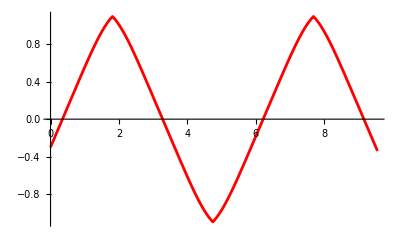

12.0396

```mathematica
f[y_]:=1.4-0.18*y^4;
n[y_,w_]:=f[y]*(1-(0.35*10^14/w)^2);
start=-40 Degree;
y0=-0.3
zCoord=8+2*Sin[17.951958020513104*y0]
radius=1.1;
accurance=radius/1000;

waveWay[a_,w_,accurance_]:=(
dist=0;
xPrev=0;
yPrev=-0.3;
x=0;
y=-0.3;
angle=a;
coords=List[];
isDirChanged=0;
direction=1;
AppendTo[coords,{x,y}];
While[
x<zCoord,

If[Abs[y-direction*radius]<accurance,direction*=-1;isDirChanged=1,
If[(n[y,w]/n[y+direction*accurance,w])*Sin[angle]>1,direction*=-1;isDirChanged=1,];
If[isDirChanged==0,angle=ArcSin[(n[y,w]/n[y+direction*accurance,w])*Sin[angle]],];
xPrev=x;
yPrev=y;
x+=Tan[angle]*accurance;
y+=direction*accurance;
dist+=Sqrt[((x-xPrev)^2+(Abs[y]-Abs[yPrev])^2)];
AppendTo[coords,{x,y}];
isDirChanged=0;
];
];
{coords,angle, dist}
);

w=3.1*10^14;
angle=90 Degree-ArcSin[f[0]/n[0,w]*Sin[start]];
results=waveWay[angle,w,accurance];
coords=results[[1]];
plot=ListLinePlot[coords,PlotStyle->{Red}];

Show[plot]
Print[results[[3]]];
```

```mathematica
-0.3
```

-0.3